```mathematica
(* Solving Newton's equations ddotx == 0, ddoty = -g gives *)
```

```mathematica
v0 = 20; g =9.81;
x[t_,θ_]:=Module[{},
t v0 Cos[θ]
]
y[t_,θ_]:=Module[{},
-g t^2/2 + v0 Sin[θ] t + 100
]
(* Time where the parabola hits the ground. *)
tint[θ_]:=Module[{},
(2 v0 Sin[θ]+√(800 g+4 v0^2 Sin[θ]^2))/(2 g)
]
```

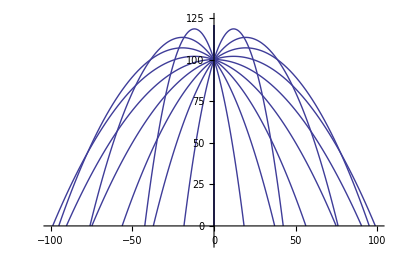

```mathematica
(* Make a plot of falling fireworks *)
nm=10;
thvl=Pi Range[-nm,nm]/nm+Pi/2;
Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

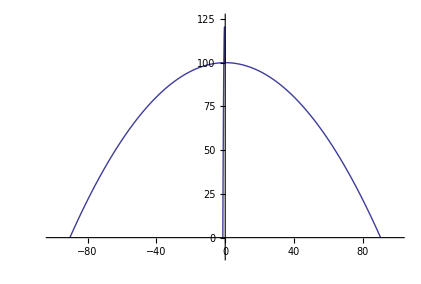

```mathematica
(* Plot of the fragments that have horizontal velocity vecs *)
nm=10;
thvl={0,Pi,Pi/2+0.01};
Show[Table[ParametricPlot[{x[t,thvl[[i]]],y[t,thvl[[i]]]},{t,0,tint[thvl[[i]]]},PlotRange->{{-100,100},{-10,125}}],{i,1,Length[thvl]}],PlotRange->{{-100,100},{-10,125}}]
```

```mathematica
(* Find the area under the base curve first using standard calculus.  Then find the lengths of the curves with θ between 0 and Pi from t = 0 until the intersect either the left or right curve.  Integrate over these arc lengths to find the upper area.  Finally find the area of the region by usuing rotation. s*)
```